```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["output_4_0_2.txt","Table"];
(*Количество элементов,количество точек,количество контуров*)
{NE,NP,NC}=data[[1]];
data1=Transpose[data[[2;;NE+1]]];
(*Номера элементов*) 
EN=data1[[1]];
(*Количество узлов в элементе*)
ENP=data1[[2,1]];
(*Номера узлов в каждом элементе*) 
EP=Transpose[data1[[3;;2+ENP]]];
(*Массив координат узлов*) 
LP=Transpose@Delete[Transpose[data[[NE+2;;NE+NP+1]]],1];
LP=Transpose@Delete[Transpose@LP,3];
(*Количество узлов в каждом контуре*) 
CPN=data[[NE+NP+2]];
(*Номера точек контуров*)
CP=Flatten@data[[NE+NP+3;;-1]];
```

```mathematica
(*Массив значений функции в узлах*) 
FValues=Import["FValues.txt", "Table"][[2;;All,2]];
(*Массив значений производной по X в узлах*)
DFNValuesX=Import["DFNValuesX.txt","Table"][[2;;All,2]];
(*Массив значений производной по Y в узлах*)
DFNValuesY=Import["DFNValuesY.txt","Table"][[2;;All,2]];
(*Массив значений интеграла в узлах*) 
IFNValues=Import["IFNValues.txt","Table"][[2;;All,2]];
(*Точка для проверки*) 
p=Import["pCheck.txt","Table"][[1]];
```

```mathematica
(*Сеточная функция*) 
FFun=Transpose[Transpose[LP]~Join~{FValues}];
(*Сеточная производная по X*) 
DFFunX=Transpose[Transpose[LP]~Join~{DFNValuesX}];
(*Сеточная производная по У*) 
DFFunY=Transpose[Transpose[LP]~Join~{DFNValuesY}];
(*Сеточный интеграл*) 
IFFun=Transpose[Transpose[LP]~Join~{IFNValues}];
```

```mathematica
(*Внутренние линии*) 
listIn=Table[Table[LP[[EP[[i,j]]]],{j,1,ENP}],{i,1,NE}];
graphIn=Graphics[{Thickness[0.0025],Black,Line[listIn]}];
(*Единый контур*) 
listCont=Table[LP[[CP[[i]]]],{i,1,CPN[[1]]}]~Join~{LP[[CP[[1]]]]};
graphCont=Graphics[{Thickness[0.0025],Black,Line[listCont]}];
(*Точка для проверки*)
graphP=Graphics[{PointSize[0.015],Red,Point[p]}];
```

```mathematica
(*Полная визуализация*)
data={FFun,DFFunX,DFFunY,IFFun};
label={"FValues","DFNValuesX","DFNValuesY","INValues"};
contV=Table[ListDensityPlot[data[[i]],PlotLegends->Automatic,PlotLabel->label[[i]],ColorFunction->"NeonColors"],{i,1,4}];
```

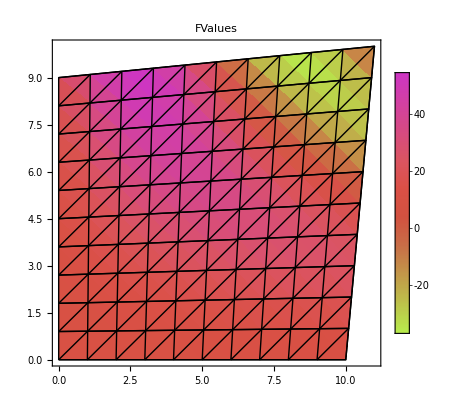

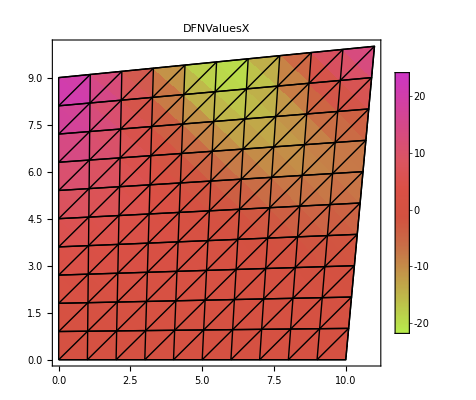

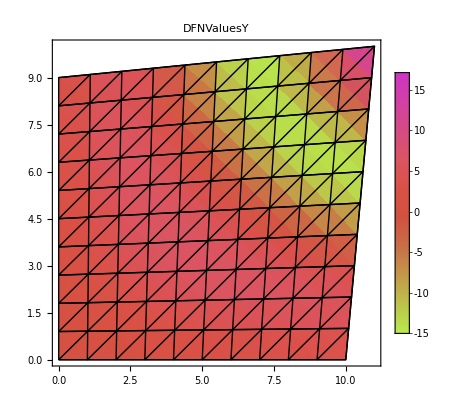

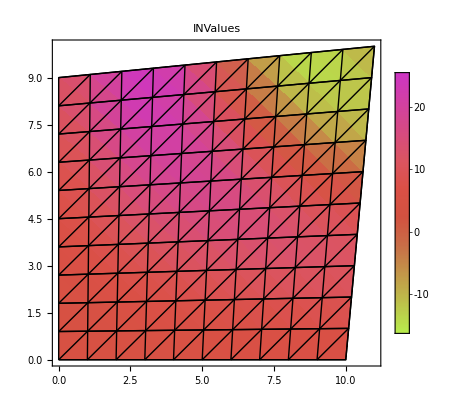

```mathematica
Table[Print@Show[{contV[[i]],graphIn,graphCont(*,graphP*)},Axes->True,AxesStyle->Directive[Black,12],ImageSize->400],{i,1,4}];
```

```mathematica
DFEX=Import["DFEValuesX.txt","Table"][[2;;,2]];
DFEY=Import["DFEValuesY.txt","Table"][[2 ;;,2]];
IFE=Import["IFEValues.txt","Table"][[2;;,2]];
```

```mathematica
MyPlotTile[f_,label_]:=Module[ {},
 {minf,maxf}=MinMax[f];
len=maxf-minf;
opac=Table [(f[[i]]-minf)/len,{i,1,Length@f}];
listInE=Table[Table[LP[[EP[[i,j]]]],{j,1,ENP}],{i,1,NE}];
graphInE=Table[Graphics[{ColorData["Rainbow"][opac[[i]]],Triangle[listInE[[i]]]}],{i,1,Length@opac} ];
leg=Print@DensityPlot[(x-minf)/len ,{x,minf,maxf},{y,0,0.1*len},ColorFunction->ColorData["NeonColors"],AspectRatio->Automatic,FrameTicks->{{None,None},{Automatic,None}}];
Print@Show [graphInE, graphIn, graphCont, PlotLabel ->label, Axes -> True, ImageSize -> 400, PlotLegends -> {leg}]
];
```

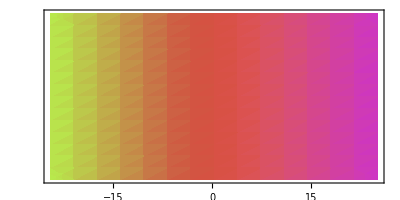

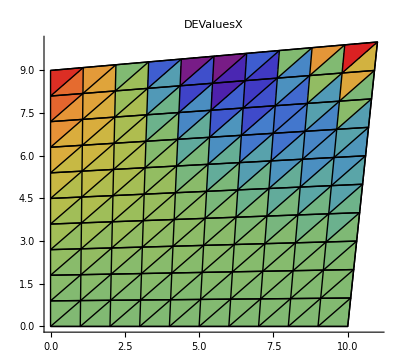

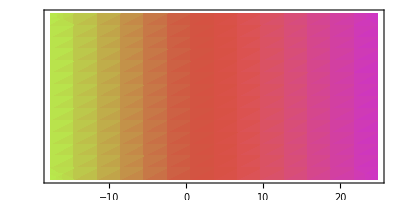

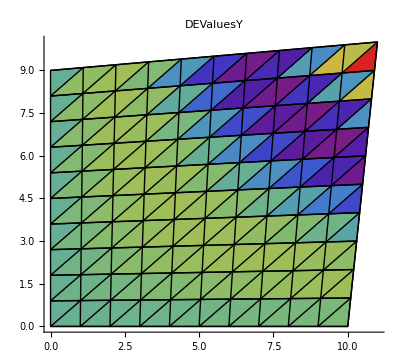

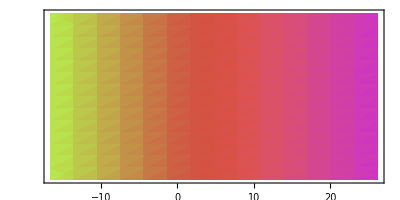

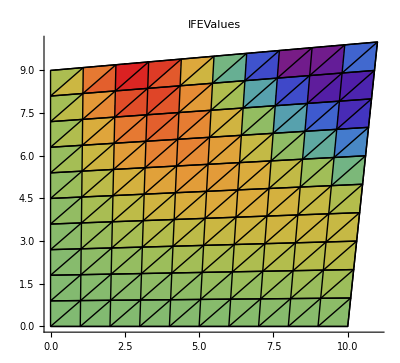

```mathematica
MyPlotTile [DFEX, "DEValuesX"]
MyPlotTile [DFEY, "DEValuesY"]
MyPlotTile [IFE, "IFEValues"]
```